```mathematica
(*Everything is an Expression!*)
```

```mathematica
(*Documentation: Core language and structure - Wolfram Language Syntax*)
```

```mathematica
head[body]
```

```mathematica
(*head - głowa wyrażenia*)
(*body - ciało wyrażenia, może się składać z kilku wyrażeń oddzielonych przecinkami*)
(*head oraz body - mogą być wyrażeniami*)
```

```mathematica
1
```

1

```mathematica
"1"
```

1

```mathematica
a
```

a

```mathematica
(**)
```

```mathematica
Hold[FullForm[a = 1]]
```

Hold[Set[a,1]]

```mathematica
Hold[FullForm[a := 1]]
```

Hold[SetDelayed[a,1]]

```mathematica
a = 1;
```

```mathematica
b = a;
```

```mathematica
c:=a;
```

```mathematica
a=10;
```

```mathematica
b
```

1

```mathematica
c
```

10

```mathematica
(*Usuwa z jądra mathematici wszystkie definicje zwiazane z a , b , c:*)
```

```mathematica
Hold[FullForm[
a=1;
b=a;
c:=a;
a = 10;
Print[a];
]]
```

Hold[CompoundExpression[Set[a,1],Set[b,a],SetDelayed[c,a],Set[a,10],Print[a],Null]]

```mathematica
Clear[a , b , c]
```

```mathematica
a=1;
b=a;
c:=a;
a = 10;
Print[a];
```

10

```mathematica
Hold[FullForm[
a=1;
b=a;
c:=a;
a = 10;
Print[a];
a+b+c
]]
```

Hold[CompoundExpression[Set[a,1],Set[b,a],SetDelayed[c,a],Set[a,10],Print[a],Plus[a,b,c]]]

```mathematica
Clear[a , b , c]
```

```mathematica
a=1;
b=a;
c:=a;
a = 10;
Print[a];
a+b+c
```

10

21

```mathematica
Out[26]
```

21

```mathematica
Hold[FullForm[a=1;b=a;c:=a;Print[a];a+b+c]]
```

Hold[CompoundExpression[Set[a,1],Set[b,a],SetDelayed[c,a],Print[a],Plus[a,b,c]]]

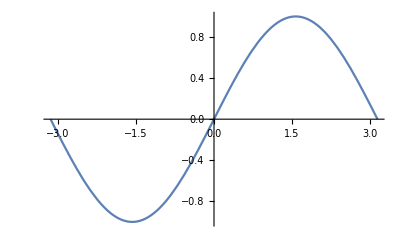

```mathematica
Plot[Sin[x] , {x , -π , π}]
```

```mathematica
(*%//FullForm*)
```

```mathematica
{1 , 2 , 3}
```

{1,2,3}

```mathematica
%//FullForm
```

List[1,2,3]

```mathematica
Module[
{a =123 , 
b = 321 , 
c},
c = a + b;
c = If[c>100 , 1 , -1];
N[-c]
]
```

-1.

```mathematica
Clear[a , b , c]
```

```mathematica
a>b
```

a>b

```mathematica
If[a>b , 1 , -1 , None]
```

None

```mathematica
If[123>100 , 1 , -1 , None]
```

1

```mathematica
i = 0;
```

```mathematica
i++
```

0

```mathematica
i
```

1

```mathematica
For[i = 0 , i <10 , i = i + 1,
Print[i];
];
```

0

1

2

3

4

5

6

7

8

9

```mathematica
Do[
Module[{a =1 , b},
b = Sin[a + i];
Print[N[b]]
];
 , {i , 0 , 9}]
```

0.841471

0.909297

0.14112

-0.756802

-0.958924

-0.279415

0.656987

0.989358

0.412118

-0.544021

```mathematica
i =0;
```

```mathematica
While[i < 10,
Print[i];
i = i + 1;
]
```

0

1

2

3

4

5

6

7

8

9

```mathematica
(*ESC + omega + ESC*)
```

```mathematica
plotRange->π//FullForm
```

Rule[plotRange,Pi]

```mathematica
f::usage = "f[ω , plotRange -> x]
Zwróci wykres funkcji ... 
";
```

```mathematica
plotRange::usage = "Zakres wykresu.";
```

```mathematica
f[ω_ , OptionsPattern[{plotRange->π}]]:= Plot[Sin[ω x] , {x , -OptionValue[plotRange] , OptionValue[plotRange]}];
```

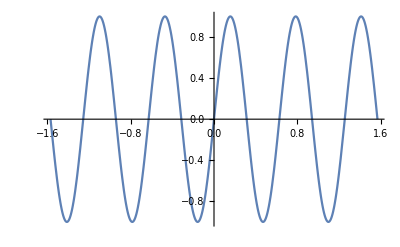

```mathematica
f[10 , plotRange->π/2]
```

```mathematica
?f
```

```mathematica
?plotRange
```

```mathematica
g::usage = "To będzie nowa funkcja,
Zwraca wykres funkcji Gaussa.";
```

```mathematica
Options[g] = {plotRange-> 10};
```

```mathematica
g[α_ , OptionsPattern[]]:=Plot[Exp[-x^2/α] , {x , -OptionValue[plotRange] , OptionValue[plotRange]} , PlotRange->All];
```

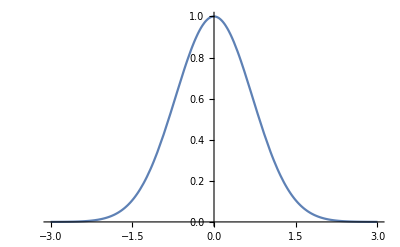

```mathematica
g[1 , plotRange->3]
```

```mathematica
(*tutorial/Patterns*)
```

```mathematica
tab = Import["https://github.com/CSSEGISandData/COVID-19/raw/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_deaths_global.csv"];
```

```mathematica
TableForm[tab[[1;;10]]]
```

Province/State | Country/Region | Lat | Long | 1/22/20 | 1/23/20 | 1/24/20 | 1/25/20 | 1/26/20 | 1/27/20 | 1/28/20 | 1/29/20 | 1/30/20 | 1/31/20 | 2/1/20 | 2/2/20 | 2/3/20 | 2/4/20 | 2/5/20 | 2/6/20 | 2/7/20 | 2/8/20 | 2/9/20 | 2/10/20 | 2/11/20 | 2/12/20 | 2/13/20 | 2/14/20 | 2/15/20 | 2/16/20 | 2/17/20 | 2/18/20 | 2/19/20 | 2/20/20 | 2/21/20 | 2/22/20 | 2/23/20 | 2/24/20 | 2/25/20 | 2/26/20 | 2/27/20 | 2/28/20 | 2/29/20 | 3/1/20 | 3/2/20 | 3/3/20 | 3/4/20 | 3/5/20 | 3/6/20 | 3/7/20 | 3/8/20 | 3/9/20 | 3/10/20 | 3/11/20 | 3/12/20 | 3/13/20 | 3/14/20 | 3/15/20 | 3/16/20 | 3/17/20 | 3/18/20 | 3/19/20 | 3/20/20 | 3/21/20 | 3/22/20 | 3/23/20 | 3/24/20 | 3/25/20 | 3/26/20 | 3/27/20 | 3/28/20 | 3/29/20 | 3/30/20 | 3/31/20 | 4/1/20 | 4/2/20 | 4/3/20 | 4/4/20 | 4/5/20 | 4/6/20 | 4/7/20 | 4/8/20 | 4/9/20 | 4/10/20 | 4/11/20 | 4/12/20 | 4/13/20 | 4/14/20 | 4/15/20 | 4/16/20 | 4/17/20 | 4/18/20 | 4/19/20 | 4/20/20 | 4/21/20 | 4/22/20 | 4/23/20 | 4/24/20 | 4/25/20 | 4/26/20 | 4/27/20 | 4/28/20 | 4/29/20 | 4/30/20 | 5/1/20 | 5/2/20 | 5/3/20 | 5/4/20 | 5/5/20 | 5/6/20 | 5/7/20 | 5/8/20 | 5/9/20 | 5/10/20 | 5/11/20 | 5/12/20 | 5/13/20 | 5/14/20 | 5/15/20 | 5/16/20 | 5/17/20 | 5/18/20 | 5/19/20 | 5/20/20 | 5/21/20 | 5/22/20 | 5/23/20 | 5/24/20 | 5/25/20 | 5/26/20 | 5/27/20 | 5/28/20 | 5/29/20 | 5/30/20 | 5/31/20 | 6/1/20 | 6/2/20 | 6/3/20 | 6/4/20 | 6/5/20 | 6/6/20 | 6/7/20 | 6/8/20 | 6/9/20 | 6/10/20 | 6/11/20 | 6/12/20 | 6/13/20 | 6/14/20 | 6/15/20 | 6/16/20 | 6/17/20 | 6/18/20 | 6/19/20 | 6/20/20 | 6/21/20 | 6/22/20 | 6/23/20 | 6/24/20 | 6/25/20 | 6/26/20 | 6/27/20 | 6/28/20 | 6/29/20 | 6/30/20 | 7/1/20 | 7/2/20 | 7/3/20 | 7/4/20 | 7/5/20 | 7/6/20 | 7/7/20 | 7/8/20 | 7/9/20 | 7/10/20 | 7/11/20 | 7/12/20 | 7/13/20 | 7/14/20 | 7/15/20 | 7/16/20 | 7/17/20 | 7/18/20 | 7/19/20 | 7/20/20 | 7/21/20 | 7/22/20 | 7/23/20 | 7/24/20 | 7/25/20 | 7/26/20 | 7/27/20 | 7/28/20 | 7/29/20 | 7/30/20 | 7/31/20 | 8/1/20 | 8/2/20 | 8/3/20 | 8/4/20 | 8/5/20 | 8/6/20 | 8/7/20 | 8/8/20 | 8/9/20 | 8/10/20 | 8/11/20 | 8/12/20 | 8/13/20 | 8/14/20 | 8/15/20 | 8/16/20 | 8/17/20 | 8/18/20 | 8/19/20 | 8/20/20 | 8/21/20 | 8/22/20 | 8/23/20 | 8/24/20 | 8/25/20 | 8/26/20 | 8/27/20 | 8/28/20 | 8/29/20 | 8/30/20 | 8/31/20 | 9/1/20 | 9/2/20 | 9/3/20 | 9/4/20 | 9/5/20 | 9/6/20 | 9/7/20 | 9/8/20 | 9/9/20 | 9/10/20 | 9/11/20 | 9/12/20 | 9/13/20 | 9/14/20 | 9/15/20 | 9/16/20 | 9/17/20 | 9/18/20 | 9/19/20 | 9/20/20 | 9/21/20 | 9/22/20 | 9/23/20 | 9/24/20 | 9/25/20 | 9/26/20 | 9/27/20 | 9/28/20 | 9/29/20 | 9/30/20 | 10/1/20 | 10/2/20 | 10/3/20 | 10/4/20 | 10/5/20 | 10/6/20 | 10/7/20 | 10/8/20 | 10/9/20 | 10/10/20 | 10/11/20 | 10/12/20 | 10/13/20 | 10/14/20
 | Afghanistan | 33.9391 | 67.71 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 6 | 6 | 7 | 7 | 11 | 14 | 14 | 15 | 15 | 18 | 18 | 21 | 23 | 25 | 30 | 30 | 30 | 33 | 36 | 36 | 40 | 42 | 43 | 47 | 50 | 57 | 58 | 60 | 64 | 68 | 72 | 85 | 90 | 95 | 104 | 106 | 109 | 115 | 120 | 122 | 127 | 132 | 136 | 153 | 168 | 169 | 173 | 178 | 187 | 193 | 205 | 216 | 218 | 219 | 220 | 227 | 235 | 246 | 249 | 257 | 265 | 270 | 294 | 300 | 309 | 327 | 357 | 369 | 384 | 405 | 426 | 446 | 451 | 471 | 478 | 491 | 504 | 546 | 548 | 569 | 581 | 598 | 618 | 639 | 675 | 683 | 703 | 721 | 733 | 746 | 774 | 807 | 819 | 826 | 864 | 898 | 920 | 936 | 957 | 971 | 994 | 1010 | 1012 | 1048 | 1094 | 1113 | 1147 | 1164 | 1181 | 1185 | 1186 | 1190 | 1211 | 1225 | 1248 | 1259 | 1269 | 1270 | 1271 | 1271 | 1272 | 1283 | 1284 | 1288 | 1288 | 1294 | 1298 | 1307 | 1312 | 1312 | 1328 | 1344 | 1354 | 1363 | 1363 | 1370 | 1375 | 1375 | 1375 | 1375 | 1385 | 1385 | 1385 | 1387 | 1389 | 1397 | 1401 | 1401 | 1402 | 1402 | 1402 | 1402 | 1406 | 1409 | 1409 | 1409 | 1409 | 1412 | 1415 | 1418 | 1420 | 1420 | 1420 | 1420 | 1420 | 1425 | 1426 | 1436 | 1436 | 1437 | 1437 | 1441 | 1444 | 1445 | 1446 | 1451 | 1451 | 1453 | 1453 | 1455 | 1458 | 1458 | 1458 | 1458 | 1462 | 1462 | 1466 | 1467 | 1469 | 1470 | 1472 | 1473 | 1477 | 1479 | 1480 | 1481
 | Albania | 41.1533 | 20.1683 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 4 | 5 | 5 | 6 | 8 | 10 | 10 | 11 | 15 | 15 | 16 | 17 | 20 | 20 | 21 | 22 | 22 | 23 | 23 | 23 | 23 | 23 | 24 | 25 | 26 | 26 | 26 | 26 | 26 | 26 | 27 | 27 | 27 | 27 | 28 | 28 | 30 | 30 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 32 | 32 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 34 | 34 | 34 | 34 | 34 | 35 | 36 | 36 | 36 | 36 | 37 | 38 | 39 | 42 | 43 | 44 | 44 | 45 | 47 | 49 | 51 | 53 | 55 | 58 | 62 | 65 | 69 | 72 | 74 | 76 | 79 | 81 | 83 | 83 | 85 | 89 | 93 | 95 | 97 | 101 | 104 | 107 | 111 | 112 | 113 | 117 | 120 | 123 | 128 | 134 | 138 | 144 | 148 | 150 | 154 | 157 | 161 | 166 | 172 | 176 | 182 | 188 | 189 | 193 | 199 | 200 | 205 | 208 | 213 | 219 | 225 | 228 | 230 | 232 | 234 | 238 | 240 | 245 | 250 | 254 | 259 | 263 | 266 | 271 | 275 | 280 | 284 | 290 | 296 | 301 | 306 | 312 | 316 | 319 | 321 | 322 | 324 | 327 | 330 | 334 | 338 | 340 | 343 | 347 | 353 | 358 | 362 | 364 | 367 | 370 | 370 | 373 | 375 | 377 | 380 | 384 | 387 | 388 | 389 | 392 | 396 | 400 | 403 | 407 | 411 | 413 | 416 | 420 | 424 | 429 | 434
 | Algeria | 28.0339 | 1.6596 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 3 | 4 | 4 | 4 | 7 | 9 | 11 | 15 | 17 | 17 | 19 | 21 | 25 | 26 | 29 | 31 | 35 | 44 | 58 | 86 | 105 | 130 | 152 | 173 | 193 | 205 | 235 | 256 | 275 | 293 | 313 | 326 | 336 | 348 | 364 | 367 | 375 | 384 | 392 | 402 | 407 | 415 | 419 | 425 | 432 | 437 | 444 | 450 | 453 | 459 | 463 | 465 | 470 | 476 | 483 | 488 | 494 | 502 | 507 | 515 | 522 | 529 | 536 | 542 | 548 | 555 | 561 | 568 | 575 | 582 | 592 | 600 | 609 | 617 | 623 | 630 | 638 | 646 | 653 | 661 | 667 | 673 | 681 | 690 | 698 | 707 | 715 | 724 | 732 | 741 | 751 | 760 | 767 | 777 | 788 | 799 | 811 | 825 | 837 | 845 | 852 | 861 | 869 | 878 | 885 | 892 | 897 | 905 | 912 | 920 | 928 | 937 | 946 | 952 | 959 | 968 | 978 | 988 | 996 | 1004 | 1011 | 1018 | 1028 | 1040 | 1052 | 1057 | 1068 | 1078 | 1087 | 1100 | 1111 | 1124 | 1136 | 1146 | 1155 | 1163 | 1174 | 1186 | 1200 | 1210 | 1223 | 1231 | 1239 | 1248 | 1261 | 1273 | 1282 | 1293 | 1302 | 1312 | 1322 | 1333 | 1341 | 1351 | 1360 | 1370 | 1379 | 1391 | 1402 | 1411 | 1418 | 1424 | 1435 | 1446 | 1456 | 1465 | 1475 | 1483 | 1491 | 1501 | 1510 | 1518 | 1523 | 1529 | 1539 | 1549 | 1556 | 1562 | 1571 | 1581 | 1591 | 1599 | 1605 | 1612 | 1620 | 1632 | 1645 | 1654 | 1659 | 1665 | 1672 | 1679 | 1689 | 1698 | 1703 | 1707 | 1711 | 1714 | 1719 | 1726 | 1736 | 1741 | 1749 | 1756 | 1760 | 1768 | 1768 | 1771 | 1783 | 1789 | 1795 | 1801 | 1809 | 1818 | 1827
 | Andorra | 42.5063 | 1.5218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 3 | 3 | 3 | 6 | 8 | 12 | 14 | 15 | 16 | 17 | 18 | 21 | 22 | 23 | 25 | 26 | 26 | 29 | 29 | 31 | 33 | 33 | 35 | 35 | 36 | 37 | 37 | 37 | 37 | 40 | 40 | 40 | 40 | 41 | 42 | 42 | 43 | 44 | 45 | 45 | 46 | 46 | 47 | 47 | 48 | 48 | 48 | 48 | 49 | 49 | 49 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 51 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 52 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 53 | 54 | 55 | 55 | 55 | 57 | 57 | 59
 | Angola | -11.2027 | 17.8739 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 6 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 10 | 10 | 10 | 10 | 11 | 11 | 13 | 15 | 17 | 18 | 19 | 19 | 19 | 21 | 21 | 22 | 23 | 23 | 26 | 26 | 26 | 27 | 28 | 29 | 29 | 29 | 29 | 30 | 33 | 33 | 35 | 39 | 40 | 41 | 47 | 48 | 51 | 52 | 54 | 55 | 58 | 59 | 62 | 64 | 67 | 70 | 75 | 78 | 80 | 80 | 80 | 86 | 86 | 88 | 88 | 90 | 92 | 93 | 94 | 94 | 96 | 100 | 102 | 103 | 105 | 106 | 107 | 107 | 108 | 109 | 112 | 113 | 115 | 117 | 117 | 120 | 124 | 126 | 130 | 131 | 132 | 134 | 136 | 139 | 143 | 144 | 147 | 147 | 152 | 154 | 155 | 159 | 162 | 167 | 171 | 174 | 176 | 179 | 183 | 185 | 189 | 193 | 195 | 199 | 211 | 211 | 208 | 212 | 218 | 218 | 219 | 222 | 227
 | Antigua and Barbuda | 17.0608 | -61.7964 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
 | Argentina | -38.4161 | -63.6167 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 6 | 8 | 9 | 13 | 18 | 19 | 23 | 27 | 28 | 36 | 39 | 43 | 44 | 48 | 56 | 63 | 72 | 82 | 83 | 90 | 97 | 102 | 111 | 115 | 123 | 129 | 132 | 136 | 147 | 152 | 165 | 176 | 185 | 192 | 197 | 207 | 214 | 218 | 225 | 237 | 246 | 260 | 264 | 273 | 282 | 293 | 300 | 305 | 314 | 319 | 329 | 353 | 356 | 363 | 373 | 382 | 393 | 403 | 416 | 433 | 445 | 452 | 467 | 484 | 500 | 508 | 520 | 528 | 539 | 556 | 569 | 583 | 608 | 632 | 648 | 664 | 693 | 717 | 735 | 765 | 785 | 815 | 833 | 854 | 878 | 913 | 948 | 979 | 992 | 1011 | 1043 | 1078 | 1116 | 1150 | 1184 | 1207 | 1232 | 1280 | 1307 | 1351 | 1385 | 1437 | 1481 | 1507 | 1582 | 1644 | 1694 | 1720 | 1774 | 1810 | 1845 | 1903 | 1968 | 2050 | 2112 | 2178 | 2220 | 2260 | 2373 | 2490 | 2588 | 2702 | 2807 | 2893 | 2939 | 3059 | 3179 | 3288 | 3441 | 3543 | 3596 | 3648 | 3813 | 3979 | 4106 | 4251 | 4411 | 4523 | 4606 | 4764 | 5004 | 5213 | 5362 | 5527 | 5637 | 5703 | 5814 | 6048 | 6330 | 6517 | 6730 | 6848 | 6985 | 7366 | 7563 | 7839 | 8050 | 8271 | 8353 | 8457 | 8660 | 8919 | 9118 | 9361 | 9623 | 9739 | 9859 | 10129 | 10405 | 10658 | 10907 | 11148 | 11263 | 11352 | 11667 | 11852 | 12116 | 12460 | 12656 | 12799 | 13053 | 13482 | 13952 | 14376 | 14766 | 15208 | 15543 | 15749 | 16113 | 16519 | 16937 | 20288 | 20599 | 20795 | 21018 | 21468 | 21827 | 22226 | 22710 | 23225 | 23581 | 23868 | 24186 | 24572 | 24921
 | Armenia | 40.0691 | 45.0382 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 3 | 3 | 3 | 4 | 7 | 7 | 7 | 7 | 8 | 8 | 9 | 10 | 12 | 13 | 13 | 14 | 16 | 17 | 18 | 19 | 20 | 20 | 22 | 24 | 24 | 24 | 27 | 28 | 28 | 29 | 30 | 30 | 32 | 33 | 33 | 35 | 39 | 40 | 40 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 52 | 55 | 60 | 61 | 64 | 67 | 70 | 74 | 77 | 81 | 87 | 91 | 98 | 113 | 120 | 127 | 131 | 139 | 158 | 170 | 176 | 183 | 190 | 200 | 211 | 217 | 227 | 245 | 258 | 264 | 269 | 285 | 293 | 302 | 309 | 319 | 332 | 350 | 360 | 372 | 386 | 397 | 410 | 421 | 426 | 433 | 443 | 453 | 459 | 469 | 477 | 484 | 491 | 503 | 521 | 535 | 546 | 559 | 565 | 573 | 581 | 592 | 607 | 620 | 631 | 641 | 650 | 662 | 678 | 688 | 692 | 700 | 705 | 711 | 719 | 723 | 728 | 738 | 749 | 754 | 762 | 768 | 770 | 772 | 777 | 785 | 791 | 796 | 803 | 806 | 809 | 814 | 817 | 818 | 824 | 832 | 833 | 836 | 842 | 850 | 852 | 854 | 858 | 861 | 864 | 869 | 872 | 877 | 879 | 881 | 884 | 887 | 891 | 895 | 897 | 900 | 903 | 905 | 906 | 909 | 911 | 916 | 919 | 920 | 923 | 925 | 926 | 928 | 930 | 936 | 938 | 942 | 945 | 947 | 948 | 951 | 957 | 958 | 959 | 963 | 966 | 972 | 977 | 984 | 990 | 995 | 1004 | 1010 | 1016 | 1020 | 1026 | 1032 | 1039
Australian Capital Territory | Australia | -35.4735 | 149.012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3

```mathematica
Dimensions[tab]
```

{268,271}

```mathematica
(*tab[[2]]*)
```

```mathematica
{1 , 2 , 3}[[2]]
```

2

```mathematica
Hold[FullForm[{1 , 2 , 3}[[2]]]]
```

Hold[Part[List[1,2,3],2]]

```mathematica
{1 , 2 , 3}[[2;;3]]
```

{2,3}

```mathematica
TableForm[{{"państwo" , "liczba zachorowań"} , {"Polska" , 10}}]
```

państwo | liczba zachorowań
Polska | 10

```mathematica
{{"państwo" , "liczba zachorowań"} , {"Polska" , 10}}[[2 , 2]]
```

10

```mathematica
{{"państwo" , "liczba zachorowań"} , {"Polska" , 10}}[[2]][[2]]
```

10

```mathematica
lz = Cases[tab , {_ , "Poland" , _ , _ , a__}:>{a}][[1]];
```

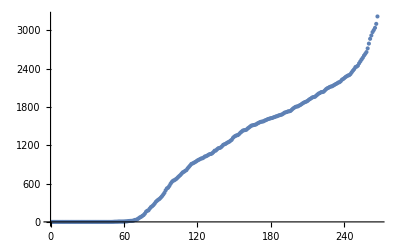

```mathematica
ListPlot[lz]
```

```mathematica
getPoland[{_ , "Poland" , _ , _ , a__}]:={a};
```

```mathematica
getPoland[{1 , 2 , 3}]
```

getPoland[{1,2,3}]

```mathematica
getPoland[{"" , "Poland" , 1 , 2 , 0 , 0 , 0 , 1 , 2 , 3 , 3 , 4}]
```

{0,0,0,1,2,3,3,4}

```mathematica
daneDlaPolski = None;
```

```mathematica
getPoland[{_ , "Poland" , _ , _ , a__}]:=(
daneDlaPolski = {a};
);
```

```mathematica
getPoland[{1 , 2 , 3}];
```

```mathematica
getPoland[{"" , "Poland" , 1 , 2 , 0 , 0 , 0 , 1 , 2 , 3 , 3 , 4}]
```

```mathematica
daneDlaPolski
```

{0,0,0,1,2,3,3,4}

```mathematica
daneDlaPolski = None;
```

```mathematica
TableForm[tab[[1;;3]]]
```

Province/State | Country/Region | Lat | Long | 1/22/20 | 1/23/20 | 1/24/20 | 1/25/20 | 1/26/20 | 1/27/20 | 1/28/20 | 1/29/20 | 1/30/20 | 1/31/20 | 2/1/20 | 2/2/20 | 2/3/20 | 2/4/20 | 2/5/20 | 2/6/20 | 2/7/20 | 2/8/20 | 2/9/20 | 2/10/20 | 2/11/20 | 2/12/20 | 2/13/20 | 2/14/20 | 2/15/20 | 2/16/20 | 2/17/20 | 2/18/20 | 2/19/20 | 2/20/20 | 2/21/20 | 2/22/20 | 2/23/20 | 2/24/20 | 2/25/20 | 2/26/20 | 2/27/20 | 2/28/20 | 2/29/20 | 3/1/20 | 3/2/20 | 3/3/20 | 3/4/20 | 3/5/20 | 3/6/20 | 3/7/20 | 3/8/20 | 3/9/20 | 3/10/20 | 3/11/20 | 3/12/20 | 3/13/20 | 3/14/20 | 3/15/20 | 3/16/20 | 3/17/20 | 3/18/20 | 3/19/20 | 3/20/20 | 3/21/20 | 3/22/20 | 3/23/20 | 3/24/20 | 3/25/20 | 3/26/20 | 3/27/20 | 3/28/20 | 3/29/20 | 3/30/20 | 3/31/20 | 4/1/20 | 4/2/20 | 4/3/20 | 4/4/20 | 4/5/20 | 4/6/20 | 4/7/20 | 4/8/20 | 4/9/20 | 4/10/20 | 4/11/20 | 4/12/20 | 4/13/20 | 4/14/20 | 4/15/20 | 4/16/20 | 4/17/20 | 4/18/20 | 4/19/20 | 4/20/20 | 4/21/20 | 4/22/20 | 4/23/20 | 4/24/20 | 4/25/20 | 4/26/20 | 4/27/20 | 4/28/20 | 4/29/20 | 4/30/20 | 5/1/20 | 5/2/20 | 5/3/20 | 5/4/20 | 5/5/20 | 5/6/20 | 5/7/20 | 5/8/20 | 5/9/20 | 5/10/20 | 5/11/20 | 5/12/20 | 5/13/20 | 5/14/20 | 5/15/20 | 5/16/20 | 5/17/20 | 5/18/20 | 5/19/20 | 5/20/20 | 5/21/20 | 5/22/20 | 5/23/20 | 5/24/20 | 5/25/20 | 5/26/20 | 5/27/20 | 5/28/20 | 5/29/20 | 5/30/20 | 5/31/20 | 6/1/20 | 6/2/20 | 6/3/20 | 6/4/20 | 6/5/20 | 6/6/20 | 6/7/20 | 6/8/20 | 6/9/20 | 6/10/20 | 6/11/20 | 6/12/20 | 6/13/20 | 6/14/20 | 6/15/20 | 6/16/20 | 6/17/20 | 6/18/20 | 6/19/20 | 6/20/20 | 6/21/20 | 6/22/20 | 6/23/20 | 6/24/20 | 6/25/20 | 6/26/20 | 6/27/20 | 6/28/20 | 6/29/20 | 6/30/20 | 7/1/20 | 7/2/20 | 7/3/20 | 7/4/20 | 7/5/20 | 7/6/20 | 7/7/20 | 7/8/20 | 7/9/20 | 7/10/20 | 7/11/20 | 7/12/20 | 7/13/20 | 7/14/20 | 7/15/20 | 7/16/20 | 7/17/20 | 7/18/20 | 7/19/20 | 7/20/20 | 7/21/20 | 7/22/20 | 7/23/20 | 7/24/20 | 7/25/20 | 7/26/20 | 7/27/20 | 7/28/20 | 7/29/20 | 7/30/20 | 7/31/20 | 8/1/20 | 8/2/20 | 8/3/20 | 8/4/20 | 8/5/20 | 8/6/20 | 8/7/20 | 8/8/20 | 8/9/20 | 8/10/20 | 8/11/20 | 8/12/20 | 8/13/20 | 8/14/20 | 8/15/20 | 8/16/20 | 8/17/20 | 8/18/20 | 8/19/20 | 8/20/20 | 8/21/20 | 8/22/20 | 8/23/20 | 8/24/20 | 8/25/20 | 8/26/20 | 8/27/20 | 8/28/20 | 8/29/20 | 8/30/20 | 8/31/20 | 9/1/20 | 9/2/20 | 9/3/20 | 9/4/20 | 9/5/20 | 9/6/20 | 9/7/20 | 9/8/20 | 9/9/20 | 9/10/20 | 9/11/20 | 9/12/20 | 9/13/20 | 9/14/20 | 9/15/20 | 9/16/20 | 9/17/20 | 9/18/20 | 9/19/20 | 9/20/20 | 9/21/20 | 9/22/20 | 9/23/20 | 9/24/20 | 9/25/20 | 9/26/20 | 9/27/20 | 9/28/20 | 9/29/20 | 9/30/20 | 10/1/20 | 10/2/20 | 10/3/20 | 10/4/20 | 10/5/20 | 10/6/20 | 10/7/20 | 10/8/20 | 10/9/20 | 10/10/20 | 10/11/20 | 10/12/20 | 10/13/20 | 10/14/20
 | Afghanistan | 33.9391 | 67.71 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 6 | 6 | 7 | 7 | 11 | 14 | 14 | 15 | 15 | 18 | 18 | 21 | 23 | 25 | 30 | 30 | 30 | 33 | 36 | 36 | 40 | 42 | 43 | 47 | 50 | 57 | 58 | 60 | 64 | 68 | 72 | 85 | 90 | 95 | 104 | 106 | 109 | 115 | 120 | 122 | 127 | 132 | 136 | 153 | 168 | 169 | 173 | 178 | 187 | 193 | 205 | 216 | 218 | 219 | 220 | 227 | 235 | 246 | 249 | 257 | 265 | 270 | 294 | 300 | 309 | 327 | 357 | 369 | 384 | 405 | 426 | 446 | 451 | 471 | 478 | 491 | 504 | 546 | 548 | 569 | 581 | 598 | 618 | 639 | 675 | 683 | 703 | 721 | 733 | 746 | 774 | 807 | 819 | 826 | 864 | 898 | 920 | 936 | 957 | 971 | 994 | 1010 | 1012 | 1048 | 1094 | 1113 | 1147 | 1164 | 1181 | 1185 | 1186 | 1190 | 1211 | 1225 | 1248 | 1259 | 1269 | 1270 | 1271 | 1271 | 1272 | 1283 | 1284 | 1288 | 1288 | 1294 | 1298 | 1307 | 1312 | 1312 | 1328 | 1344 | 1354 | 1363 | 1363 | 1370 | 1375 | 1375 | 1375 | 1375 | 1385 | 1385 | 1385 | 1387 | 1389 | 1397 | 1401 | 1401 | 1402 | 1402 | 1402 | 1402 | 1406 | 1409 | 1409 | 1409 | 1409 | 1412 | 1415 | 1418 | 1420 | 1420 | 1420 | 1420 | 1420 | 1425 | 1426 | 1436 | 1436 | 1437 | 1437 | 1441 | 1444 | 1445 | 1446 | 1451 | 1451 | 1453 | 1453 | 1455 | 1458 | 1458 | 1458 | 1458 | 1462 | 1462 | 1466 | 1467 | 1469 | 1470 | 1472 | 1473 | 1477 | 1479 | 1480 | 1481
 | Albania | 41.1533 | 20.1683 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 4 | 5 | 5 | 6 | 8 | 10 | 10 | 11 | 15 | 15 | 16 | 17 | 20 | 20 | 21 | 22 | 22 | 23 | 23 | 23 | 23 | 23 | 24 | 25 | 26 | 26 | 26 | 26 | 26 | 26 | 27 | 27 | 27 | 27 | 28 | 28 | 30 | 30 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 32 | 32 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 34 | 34 | 34 | 34 | 34 | 35 | 36 | 36 | 36 | 36 | 37 | 38 | 39 | 42 | 43 | 44 | 44 | 45 | 47 | 49 | 51 | 53 | 55 | 58 | 62 | 65 | 69 | 72 | 74 | 76 | 79 | 81 | 83 | 83 | 85 | 89 | 93 | 95 | 97 | 101 | 104 | 107 | 111 | 112 | 113 | 117 | 120 | 123 | 128 | 134 | 138 | 144 | 148 | 150 | 154 | 157 | 161 | 166 | 172 | 176 | 182 | 188 | 189 | 193 | 199 | 200 | 205 | 208 | 213 | 219 | 225 | 228 | 230 | 232 | 234 | 238 | 240 | 245 | 250 | 254 | 259 | 263 | 266 | 271 | 275 | 280 | 284 | 290 | 296 | 301 | 306 | 312 | 316 | 319 | 321 | 322 | 324 | 327 | 330 | 334 | 338 | 340 | 343 | 347 | 353 | 358 | 362 | 364 | 367 | 370 | 370 | 373 | 375 | 377 | 380 | 384 | 387 | 388 | 389 | 392 | 396 | 400 | 403 | 407 | 411 | 413 | 416 | 420 | 424 | 429 | 434

```mathematica
Map[getPoland , tab];
```

```mathematica
daneDlaPolski
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,3,3,4,5,5,5,5,5,7,8,10,14,16,16,18,22,31,33,43,57,71,79,94,107,129,159,174,181,208,232,245,263,286,314,332,347,360,380,401,426,454,494,524,535,562,596,624,644,651,664,678,698,716,733,755,776,785,800,811,839,861,883,907,915,925,936,948,962,972,982,993,996,1007,1024,1028,1038,1051,1061,1064,1074,1092,1115,1117,1137,1153,1157,1166,1183,1206,1215,1222,1237,1247,1256,1272,1286,1316,1334,1346,1356,1359,1375,1396,1412,1429,1435,1438,1444,1463,1477,1492,1507,1512,1517,1521,1528,1542,1551,1562,1568,1571,1576,1588,1594,1605,1612,1618,1624,1627,1636,1642,1651,1655,1664,1671,1676,1682,1694,1709,1716,1721,1731,1732,1738,1756,1774,1787,1800,1807,1809,1821,1830,1844,1858,1869,1877,1885,1896,1913,1925,1938,1951,1955,1960,1977,1994,2010,2018,2032,2033,2039,2058,2078,2092,2100,2113,2120,2124,2136,2147,2159,2169,2182,2188,2203,2227,2237,2253,2270,2282,2293,2298,2316,2344,2369,2392,2424,2432,2447,2483,2513,2543,2570,2604,2630,2659,2717,2792,2867,2919,2972,3004,3039,3101,3217}

```mathematica
(*guide/GraphicsObjects*)
```

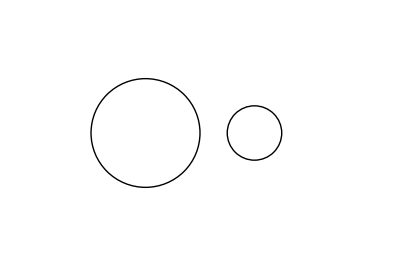

```mathematica
Graphics[
{
Circle[{0 , 0} ,1] , Circle[{2 , 0} , 0.5]
},
(*zmiana zakresu:*)
PlotRange->{{-2 , 4} , {-2 , 2}}
]
```

```mathematica
fac[n_/;n>0]:=n!;
```

```mathematica
Clear[fac]
```

```mathematica
fac[n_]:=n!/;n>0;
```

```mathematica
fac[-1]
```

fac[-1]

```mathematica
fac[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
fac[10]
```

3628800

```mathematica
10//fac
```

3628800

```mathematica
bin[a_ , b_]:=a*b/;a<0&&b>0;
```

```mathematica
bin[1 , 1]
```

bin[1,1]

```mathematica
bin[-1 , 1]
```

-1

```mathematica
(-1)~bin~1
```

-1

```mathematica
Hold[FullForm[(-1)~bin~1]]
```

Hold[bin[-1,1]]

```mathematica
onlyOne[a_]:=Print["Got only one argument: "<>ToString[a]];
```

```mathematica
onlyOne[1]
```

Got only one argument: 1

```mathematica
onlyOne[1 , 2 , 3]
```

onlyOne[1,2,3]

```mathematica
oneOrMore[a__]:=Print["Got one or more: "<>ToString[{a}]];
```

```mathematica
oneOrMore[]
```

oneOrMore[]

```mathematica
oneOrMore[1]
```

Got one or more: {1}

```mathematica
oneOrMore[1 , 2]
```

Got one or more: {1, 2}

```mathematica
zeroOrMore[a___]:=Print["Got zero or more: "<>ToString[{a}]];
```

```mathematica
zeroOrMore[]
```

Got zero or more: {}

```mathematica
zeroOrMore[1]
```

Got zero or more: {1}

```mathematica
zeroOrMore[1 , 2]
```

Got zero or more: {1, 2}

```mathematica
zeroOrMore[1 , 2 ,3]
```

Got zero or more: {1, 2, 3}

```mathematica
PrimeQ[3]
```

True

```mathematica
NumberQ["123"]
```

False

```mathematica
NumberQ[123]
```

True

```mathematica
numericalFunction[x_?NumberQ]:= Sin[x];
```

```mathematica
numericalFunction["1"]
```

numericalFunction[1]

```mathematica
%//FullForm
```

numericalFunction["1"]

```mathematica
NumberQ["1"]
```

False

```mathematica
numericalFunction[1.]
```

0.841471

```mathematica
numericalFunction[1. + ⅈ]
```

1.29846+0.634964 ⅈ

```mathematica
NumberQ[1. + ⅈ]
```

True

```mathematica
isOneOrMinusOne[1|-1]= "It is!";
```

```mathematica
isOneOrMinusOne[1]
```

It is!

```mathematica
isOneOrMinusOne[-1]
```

It is!

```mathematica
isOneOrMinusOne[123]
```

isOneOrMinusOne[123]

```mathematica
{1 , 2 , 3}
```

{1,2,3}

```mathematica
Table[element[i , j] , {i , 1 , 3} , {j , 1 , 3}]
```

{{element[1,1],element[1,2],element[1,3]},{element[2,1],element[2,2],element[2,3]},{element[3,1],element[3,2],element[3,3]}}

```mathematica
%//TableForm
```

element[1,1] | element[1,2] | element[1,3]
element[2,1] | element[2,2] | element[2,3]
element[3,1] | element[3,2] | element[3,3]

```mathematica
Table[element[i , j] , {i , 1 , 3} , {j , 1 , 3}]//MatrixForm
```

(element[1,1] | element[1,2] | element[1,3]
element[2,1] | element[2,2] | element[2,3]
element[3,1] | element[3,2] | element[3,3])

```mathematica
Table[i , {i , 1 , 10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Array[function, {10}]
```

{function[1],function[2],function[3],function[4],function[5],function[6],function[7],function[8],function[9],function[10]}

```mathematica
Array[function, {3 , 3}]
```

{{function[1,1],function[1,2],function[1,3]},{function[2,1],function[2,2],function[2,3]},{function[3,1],function[3,2],function[3,3]}}